```mathematica
SetDirectory["C:\\Users\\brenton\\DeadlockWorkspace\\transcripts\\"]
```

C:\Users\brenton\DeadlockWorkspace\transcripts

```mathematica
names=FileNames["transcript-*.txt",""];
```

```mathematica
counts={#,Flatten[StringCases[ReadList[#,String],"hardest is "~~Shortest[a__]~~" moves":>ToExpression[a]]]}&/@names;
```

```mathematica
Sort[Flatten[counts[[All,2]]]]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,«50998»,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,65,65,65,65,65,65,65,65,65,65,65,65,66,66,66,66,66,66,66,66,66,66,66,67,67,67,67,67,67,67,67,67,67,68,68,68,68,68,69,69,69,70,70,70,71,71,71,71,71,71,71,71,71,71,72,72,73,73,74,74,74,74,74,74,74,74,75,75,76,76,76,76,76,76,76,77,77,77,77,78,78,78,78,81,81,82,82,82,84,85,85,87,87,88,89,89,90,99}

```mathematica
Total[Length[#[[2]]]&/@counts]
```

51234

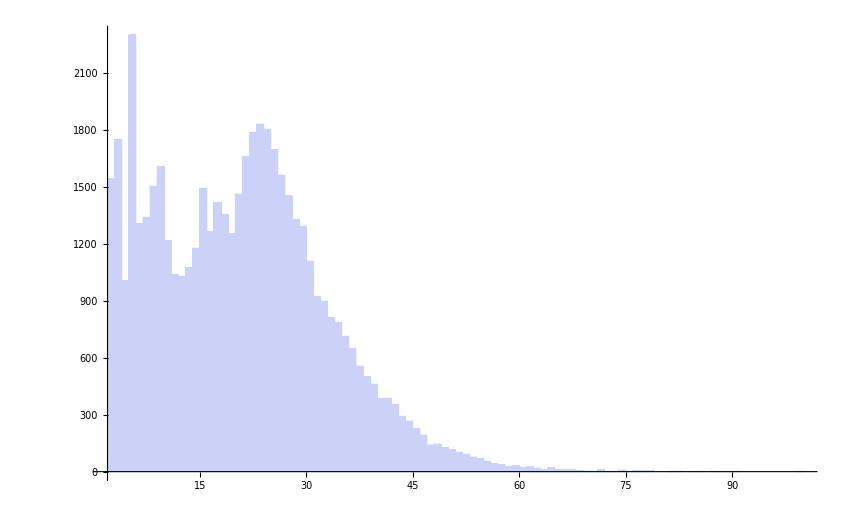

```mathematica
Histogram[Flatten[counts[[All,2]]]]
```

```mathematica
firstBoardChar[s_String]:=StringMatchQ[StringTake[s,1],"/"|"|"|"\\"|"Y"|"J"|"K"]
```

```mathematica
readBoardsFromTranscript[f_]:=(
Reap[
id=StringDrop[StringDrop[f,11],-4];
Pint[id];
Catch[
While[True,
r=Read[f,String];
Which[
r===EndOfFile,Break[],
StringMatchQ[r,"generating partition #"~~__],(
p=StringCases[r,"generating partition #"~~p__:>p][[1]];
Pint["partition "<>p];
r=Read[f,String];
Which[
StringMatchQ[r,"idhash "~~__~~"hardest is "~~(NumberString)~~__],(
moves=StringCases[r,"idhash "~~__~~"hardest is "~~m:NumberString~~__:>m][[1]];
board=Read[f,{String,String,String,String,String,String,String,String}];
If[And@@(firstBoardChar/@board),Sow[{{"id"->id,"partition"->p,"moves"->moves},board}],Throw[{"not a board",board},1]]
),
StringMatchQ[r,"idhash "~~__~~"hardest is null"~~__],Null,
True,Throw[{"1",r},1]
]
)
]
]
,
1
,
Print["bad",#]&
];
Close[f];
Null
][[2,1]]
)
```

```mathematica
readBoardsFromTranscript[names[[1]]]
```

{{{id→0-4-1,partition→0,moves→21},{/------\,|   R A|,|BBBR A|,|  CCCA|,|  D   |,|  D   |,J  D   Y,\---J--/}},{{id→0-4-1,partition→1,moves→13},{/------\,|   R  |,|   R  |,|      |,| AB CD|,| AB CD|,J AB CDY,\---J--/}},{{id→0-4-1,partition→2,moves→15},{/------\,|   R  |,|   R  |,|   AAA|,| BBBCD|,|    CD|,J    CDY,\---J--/}},{{id→0-4-1,partition→3,moves→12},{/------\,|   RAB|,|CCCRAB|,|    AB|,|   DDD|,|      |,J      Y,\---J--/}},{{id→0-4-1,partition→4,moves→16},{/------\,|AAAR  |,|   R  |,|      |,| BC   |,| BCDDD|,J BC   Y,\---J--/}},{{id→0-4-1,partition→5,moves→27},{/------\,|ABCR  |,|ABCR  |,|ABCDDD|,|      |,|      |,J      Y,\---J--/}},{{id→0-4-1,partition→6,moves→21},{/------\,|AAAR  |,| BCR  |,| BCDDD|,| BC   |,|      |,J      Y,\---J--/}},{{id→0-4-1,partition→7,moves→12},{/------\,|AAAR  |,|   R  |,|      |,|  B CD|,|  B CD|,J  B CDY,\---J--/}},{{id→0-4-1,partition→8,moves→15},{/------\,|AAAR  |,|   R  |,|   BBB|,|     C|,|  DDDC|,J     CY,\---J--/}},{{id→0-4-1,partition→9,moves→15},{/------\,|   R  |,|AAAR  |,|   BBB|,|  CCCD|,|     D|,J     DY,\---J--/}},{{id→0-4-1,partition→10,moves→21},{/------\,|AAAR  |,|   R  |,|      |,| BCDDD|,| BC   |,J BC   Y,\---J--/}},{{id→0-4-1,partition→11,moves→21},{/------\,|AAAR  |,|   R  |,|      |,|  BCCC|,|  BDDD|,J  B   Y,\---J--/}},{{id→0-4-1,partition→12,moves→15},{/------\,|   R  |,|AAAR  |,|   BBB|,|     C|,|  DDDC|,J     CY,\---J--/}},{{id→0-4-1,partition→13,moves→11},{/------\,|AAAR  |,|BBBR  |,|      |,|    CD|,|    CD|,J    CDY,\---J--/}},{{id→0-4-1,partition→14,moves→17},{/------\,|AAAR  |,|BBBR  |,|      |,|  C   |,|  CDDD|,J  C   Y,\---J--/}},{{id→0-4-1,partition→15,moves→15},{/------\,|AAAR  |,|   R  |,|   BBB|,|  CCCD|,|     D|,J     DY,\---J--/}},{{id→0-4-1,partition→16,moves→17},{/------\,|   R A|,|   R A|,|  BBBA|,|   CCC|,|   DDD|,J      Y,\---J--/}},{{id→0-4-1,partition→17,moves→17},{/------\,|AAAR  |,|BBBR  |,|  CDDD|,|  C   |,|  C   |,J      Y,\---J--/}},{{id→0-4-1,partition→18,moves→15},{/------\,|   R A|,|BBBR A|,|     A|,|   CCC|,|   DDD|,J      Y,\---J--/}},{{id→0-4-1,partition→19,moves→12},{/------\,|   R  |,|AAAR  |,|      |,|  B CD|,|  B CD|,J  B CDY,\---J--/}},{{id→0-4-1,partition→20,moves→21},{/------\,|   R  |,|   R  |,|      |,|ABCDDD|,|ABC   |,JABC   Y,\---J--/}},{{id→0-4-1,partition→21,moves→19},{/------\,|   R  |,|AAAR  |,|      |,| BC   |,| BCDDD|,J BC   Y,\---J--/}},{{id→0-4-1,partition→22,moves→18},{/------\,|   R  |,|   R  |,|      |,|ABC   |,|ABCDDD|,JABC   Y,\---J--/}},{{id→0-4-1,partition→23,moves→15},{/------\,|   R  |,|   R  |,|   AAA|,|    BC|,| DDDBC|,J    BCY,\---J--/}},{{id→0-4-1,partition→24,moves→12},{/------\,|AAAR B|,|CCCR B|,|     B|,|   DDD|,|      |,J      Y,\---J--/}},{{id→0-4-1,partition→25,moves→21},{/------\,|   R  |,|   R  |,|      |,| ABCCC|,| ABDDD|,J AB   Y,\---J--/}}}

```mathematica
(
boards=readBoardsFromTranscript[#];
(
Print[#[[1]]]
)&/@boards
)&/@{names[[1]]}
```

{id→0-4-1,partition→0,moves→21}

{id→0-4-1,partition→1,moves→13}

{id→0-4-1,partition→2,moves→15}

{id→0-4-1,partition→3,moves→12}

{id→0-4-1,partition→4,moves→16}

{id→0-4-1,partition→5,moves→27}

{id→0-4-1,partition→6,moves→21}

{id→0-4-1,partition→7,moves→12}

{id→0-4-1,partition→8,moves→15}

{id→0-4-1,partition→9,moves→15}

{id→0-4-1,partition→10,moves→21}

{id→0-4-1,partition→11,moves→21}

{id→0-4-1,partition→12,moves→15}

{id→0-4-1,partition→13,moves→11}

{id→0-4-1,partition→14,moves→17}

{id→0-4-1,partition→15,moves→15}

{id→0-4-1,partition→16,moves→17}

{id→0-4-1,partition→17,moves→17}

{id→0-4-1,partition→18,moves→15}

{id→0-4-1,partition→19,moves→12}

{id→0-4-1,partition→20,moves→21}

{id→0-4-1,partition→21,moves→19}

{id→0-4-1,partition→22,moves→18}

{id→0-4-1,partition→23,moves→15}

{id→0-4-1,partition→24,moves→12}

{id→0-4-1,partition→25,moves→21}

{{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}}

```mathematica
(
boards=readBoardsFromTranscript[#];
(
rules=#[[1]];
data=#[[2]];
file="C:\\Users\\brenton\\DeadlockWorkspace\\DeadlockResources\\gen\\boards\\gen-"<>("id"/.rules)<>"-"<>("partition"/.rules)<>".dat";
(WriteString[file,"moves: "<>("moves"/.rules)];WriteString[file,"\n"]);
(WriteString[file,#];WriteString[file,"\n"])&/@data;
Close[file]
)&/@boards
)&/@names;
```

```mathematica
Total[Length/@a]
```

51234

```mathematica
Streams[]
```

{OutputStream[stdout,1],OutputStream[stderr,2]}